# Embedded Pathways

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/embedded-pathways/analysis

## Data

### Ordination

```mathematica
ordinationData=Import["../results/ordination.tsv"];
```

```mathematica
headings=ordinationData[[1]]
```

{id,umap_1,umap_2,tsne_1,tsne_2,pca_1,pca_2,pca_3,pca_4,pca_5}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,headings]
```

{id→1,umap_1→2,umap_2→3,tsne_1→4,tsne_2→5,pca_1→6,pca_2→7,pca_3→8,pca_4→9,pca_5→10}

```mathematica
ordinationData=Drop[ordinationData,1];
```

```mathematica
nodes=Union[ordinationData[[All,1]]];
```

```mathematica
toUmap1=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,2}]]];
```

```mathematica
toUmap2=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,3}]]];
```

```mathematica
toTsne1=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,4}]]];
```

```mathematica
toTsne2=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,5}]]];
```

```mathematica
toPca1=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,6}]]];
```

```mathematica
toPca2=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,7}]]];
```

```mathematica
toPca3=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,8}]]];
```

```mathematica
toPca4=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,9}]]];
```

```mathematica
toPca5=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,10}]]];
```

### Metadata

```mathematica
metadata=Import["../data/metadata.tsv"];
```

```mathematica
headings=metadata[[1]]
```

{name,parent,clade,S1_mutations}

```mathematica
metadata=Drop[metadata,1];
```

```mathematica
toParent=Map[#[[1]]->#[[2]]&,metadata[[All,{1,2}]]];
```

```mathematica
toClade=Map[#[[1]]->If[StringQ[#[[2]]],StringSplit[#[[2]]," "][[1]],"other"]&,metadata[[All,{1,3}]]];
```

```mathematica
clades=Union[toClade[[All,2]]]
```

{19A,19B,20B,20C,20D,20E,20G,20H,20I,20J,21A,21B,21C,21D,21F,21G,21H,21I,21J,21K,21L,21M,22A,22B,22C,22D,22E,22F,23A,23B,23C,23D,23E,23F,23G,23H,24A,24B,24C,24D,24E,24F,24G,24H,24I,other}

### Embeddings

```mathematica
embeddingsData=Import["../results/embeddings.tsv"];
```

```mathematica
headings=embeddingsData[[1,1;;10]]
```

{NODE_0000002,0.0964816,-0.126663,0.0613547,0.0971797,-0.107709,0.0279656,0.211645,-0.180656,-0.173457}

```mathematica
toEmbedding=Map[#[[1]]->#[[2;;-1]]&,embeddingsData];
```

## Clade colors

Download with “nextstrain remote download https://nextstrain.org/ncov/gisaid/global/all-time”

```mathematica
treeJson=Import["../data/ncov_gisaid_global_all-time.json","RawJSON"];
```

```mathematica
metaColorMapping=Map[StringSplit[#[[1]]," "][[1]]->RGBColor[#[[2]]]&,FirstCase[treeJson["meta"]["colorings"],x_/;x["key"]=="clade_membership"]["scale"]]
```

{20H→RGBColor[0.3686274509803922, 0.11372549019607843, 0.615686274509804],20I→RGBColor[0.30980392156862746, 0.12156862745098039, 0.6705882352941176],20J→RGBColor[0.2823529411764706, 0.16862745098039217, 0.7137254901960784],21A→RGBColor[0.25882352941176473, 0.21176470588235294, 0.7568627450980392],21I→RGBColor[0.24705882352941178, 0.2627450980392157, 0.7843137254901961],21J→RGBColor[0.24705882352941178, 0.3215686274509804, 0.8],21B→RGBColor[0.24705882352941178, 0.37254901960784315, 0.8156862745098039],21C→RGBColor[0.2549019607843137, 0.42745098039215684, 0.807843137254902],21D→RGBColor[0.2627450980392157, 0.47843137254901963, 0.803921568627451],21F→RGBColor[0.2784313725490196, 0.5215686274509804, 0.7803921568627451],21G→RGBColor[0.29411764705882354, 0.5607843137254902, 0.7568627450980392],21H→RGBColor[0.3137254901960784, 0.596078431372549, 0.7254901960784313],21K→RGBColor[0.33725490196078434, 0.6274509803921569, 0.6862745098039216],21L→RGBColor[0.3607843137254902, 0.6549019607843137, 0.6470588235294118],22A→RGBColor[0.38823529411764707, 0.6745098039215687, 0.6039215686274509],22B→RGBColor[0.41568627450980394, 0.6941176470588235, 0.5607843137254902],22C→RGBColor[0.4470588235294118, 0.7058823529411765, 0.5176470588235295],22D→RGBColor[0.4823529411764706, 0.7176470588235294, 0.47843137254901963],22E→RGBColor[0.5176470588235295, 0.7294117647058823, 0.4392156862745098],22F→RGBColor[0.5568627450980392, 0.7372549019607844, 0.403921568627451],23A→RGBColor[0.592156862745098, 0.7411764705882353, 0.3686274509803922],23B→RGBColor[0.6352941176470588, 0.7450980392156863, 0.3411764705882353],23C→RGBColor[0.6745098039215687, 0.7411764705882353, 0.3176470588235294],23D→RGBColor[0.7137254901960784, 0.7411764705882353, 0.29411764705882354],23E→RGBColor[0.7490196078431373, 0.7333333333333333, 0.2784313725490196],23F→RGBColor[0.788235294117647, 0.7215686274509804, 0.2627450980392157],23G→RGBColor[0.8156862745098039, 0.7058823529411765, 0.2549019607843137],23H→RGBColor[0.8431372549019608, 0.6823529411764706, 0.24313725490196078],23I→RGBColor[0.8705882352941177, 0.6588235294117647, 0.23529411764705882],24A→RGBColor[0.8823529411764706, 0.6235294117647059, 0.2235294117647059],24B→RGBColor[0.8980392156862745, 0.5843137254901961, 0.21568627450980393],24C→RGBColor[0.9019607843137255, 0.5333333333333333, 0.20784313725490197],24D→RGBColor[0.9019607843137255, 0.4823529411764706, 0.19607843137254902],24E→RGBColor[0.8980392156862745, 0.4235294117647059, 0.1843137254901961],24F→RGBColor[0.8862745098039215, 0.3568627450980392, 0.17254901960784313],24G→RGBColor[0.8784313725490196, 0.2901960784313726, 0.1607843137254902],24H→RGBColor[0.8705882352941177, 0.2235294117647059, 0.14901960784313725],24I→RGBColor[0.8588235294117647, 0.1568627450980392, 0.13725490196078433]}

Non-variant clades need to be assigned grays

```mathematica
earlyColorMapping=MapThread[#1->#2&,{{"19A","19B","20A","20B","20C","20D","20E","20F","20G","21F","other"},Table[GrayLevel[x],{x,0.25,0.75,0.5/10}]}]
```

{19A→GrayLevel[0.25],19B→GrayLevel[0.3],20A→GrayLevel[0.35],20B→GrayLevel[0.4],20C→GrayLevel[0.45],20D→GrayLevel[0.5],20E→GrayLevel[0.55],20F→GrayLevel[0.6000000000000001],20G→GrayLevel[0.65],21F→GrayLevel[0.7],other→GrayLevel[0.75]}

```mathematica
cladeToColor=Join[earlyColorMapping,metaColorMapping]
```

{19A→GrayLevel[0.25],19B→GrayLevel[0.3],20A→GrayLevel[0.35],20B→GrayLevel[0.4],20C→GrayLevel[0.45],20D→GrayLevel[0.5],20E→GrayLevel[0.55],20F→GrayLevel[0.6000000000000001],20G→GrayLevel[0.65],21F→GrayLevel[0.7],other→GrayLevel[0.75],20H→RGBColor[0.3686274509803922, 0.11372549019607843, 0.615686274509804],20I→RGBColor[0.30980392156862746, 0.12156862745098039, 0.6705882352941176],20J→RGBColor[0.2823529411764706, 0.16862745098039217, 0.7137254901960784],21A→RGBColor[0.25882352941176473, 0.21176470588235294, 0.7568627450980392],21I→RGBColor[0.24705882352941178, 0.2627450980392157, 0.7843137254901961],21J→RGBColor[0.24705882352941178, 0.3215686274509804, 0.8],21B→RGBColor[0.24705882352941178, 0.37254901960784315, 0.8156862745098039],21C→RGBColor[0.2549019607843137, 0.42745098039215684, 0.807843137254902],21D→RGBColor[0.2627450980392157, 0.47843137254901963, 0.803921568627451],21F→RGBColor[0.2784313725490196, 0.5215686274509804, 0.7803921568627451],21G→RGBColor[0.29411764705882354, 0.5607843137254902, 0.7568627450980392],21H→RGBColor[0.3137254901960784, 0.596078431372549, 0.7254901960784313],21K→RGBColor[0.33725490196078434, 0.6274509803921569, 0.6862745098039216],21L→RGBColor[0.3607843137254902, 0.6549019607843137, 0.6470588235294118],22A→RGBColor[0.38823529411764707, 0.6745098039215687, 0.6039215686274509],22B→RGBColor[0.41568627450980394, 0.6941176470588235, 0.5607843137254902],22C→RGBColor[0.4470588235294118, 0.7058823529411765, 0.5176470588235295],22D→RGBColor[0.4823529411764706, 0.7176470588235294, 0.47843137254901963],22E→RGBColor[0.5176470588235295, 0.7294117647058823, 0.4392156862745098],22F→RGBColor[0.5568627450980392, 0.7372549019607844, 0.403921568627451],23A→RGBColor[0.592156862745098, 0.7411764705882353, 0.3686274509803922],23B→RGBColor[0.6352941176470588, 0.7450980392156863, 0.3411764705882353],23C→RGBColor[0.6745098039215687, 0.7411764705882353, 0.3176470588235294],23D→RGBColor[0.7137254901960784, 0.7411764705882353, 0.29411764705882354],23E→RGBColor[0.7490196078431373, 0.7333333333333333, 0.2784313725490196],23F→RGBColor[0.788235294117647, 0.7215686274509804, 0.2627450980392157],23G→RGBColor[0.8156862745098039, 0.7058823529411765, 0.2549019607843137],23H→RGBColor[0.8431372549019608, 0.6823529411764706, 0.24313725490196078],23I→RGBColor[0.8705882352941177, 0.6588235294117647, 0.23529411764705882],24A→RGBColor[0.8823529411764706, 0.6235294117647059, 0.2235294117647059],24B→RGBColor[0.8980392156862745, 0.5843137254901961, 0.21568627450980393],24C→RGBColor[0.9019607843137255, 0.5333333333333333, 0.20784313725490197],24D→RGBColor[0.9019607843137255, 0.4823529411764706, 0.19607843137254902],24E→RGBColor[0.8980392156862745, 0.4235294117647059, 0.1843137254901961],24F→RGBColor[0.8862745098039215, 0.3568627450980392, 0.17254901960784313],24G→RGBColor[0.8784313725490196, 0.2901960784313726, 0.1607843137254902],24H→RGBColor[0.8705882352941177, 0.2235294117647059, 0.14901960784313725],24I→RGBColor[0.8588235294117647, 0.1568627450980392, 0.13725490196078433]}

```mathematica
variantLegend=SwatchLegend[Table[clade/.cladeToColor,{clade,clades}],Table[clade,{clade,clades}],LegendLayout->{"Row",1}];
```

```mathematica
smallVariantLegend=SwatchLegend[Table[clade/.cladeToColor,{clade,clades}],Table[clade,{clade,clades}],LegendLayout->{"Column",1},LabelStyle->{FontSize->10}];
```

## Ordinations

```mathematica
figFromOrdinationRules[dimen1_,dimen2_,xLabel_,yLabel_]:=Module[{points,lines,colors,pointFig,lineFig},
points=Table[Tooltip[{node/.dimen1,node/.dimen2},node],{node,nodes}];
lines=Table[With[{parent=node/.toParent},{{node/.dimen1,node/.dimen2},{parent/.dimen1,parent/.dimen2}}],{node,nodes}];
colors=Table[node/.toClade/.cladeToColor,{node,nodes}];
pointFig=ListPlot[Map[{#}&,points],PlotTheme->"FulLAxes",PlotRange->All,ImageSize->400,Frame->{True,True,False,False},FrameLabel->{xLabel,yLabel},Axes->False,PlotStyle->colors,PlotMarkers->{"•",Small}];
lineFig=ListLinePlot[lines,PlotTheme->"FulLAxes",PlotRange->All,ImageSize->400,Frame->{True,True,False,False},FrameLabel->{xLabel,yLabel},Axes->False,PlotStyle->Directive[AbsoluteThickness[1],Opacity[0.25],GrayLevel[0.25]]];
Show[lineFig,pointFig]
]
```

```mathematica
pca12Fig=figFromOrdinationRules[toPca1,toPca2,"PCA dimen 1", "PCA dimen 2"];
```

```mathematica
pca13Fig=figFromOrdinationRules[toPca1,toPca3,"PCA dimen 1", "PCA dimen 3"];
```

```mathematica
pca14Fig=figFromOrdinationRules[toPca1,toPca4,"PCA dimen 1", "PCA dimen 4"];
```

```mathematica
pca23Fig=figFromOrdinationRules[toPca2,toPca3,"PCA dimen 2", "PCA dimen 3"];
```

```mathematica
pca24Fig=figFromOrdinationRules[toPca2,toPca4,"PCA dimen 2", "PCA dimen 4"];
```

```mathematica
pca34Fig=figFromOrdinationRules[toPca3,toPca4,"PCA dimen 3", "PCA dimen 4"];
```

```mathematica
fig=Grid[{{pca12Fig,"",""},{pca13Fig,pca23Fig,""},{pca14Fig,pca24Fig,pca34Fig}}];
```

```mathematica
fig=Export["figures/pca_grid.png",fig,"PNG",ImageResolution->300]
```

figures/pca_grid.png

## Direct embeddings

```mathematica
embeddingStandardDeviations=Map[StandardDeviation,Transpose[Table[node/.toEmbedding,{node,nodes}]]];
```

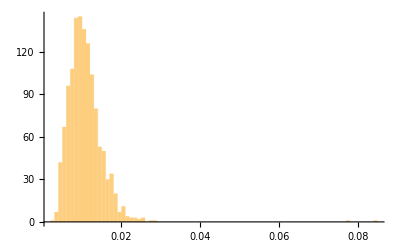

```mathematica
Histogram[embeddingStandardDeviations,100,PlotRange->All]
```

```mathematica
pos=Position[embeddingStandardDeviations,x_/;x>0.02]
```

{{75},{91},{232},{235},{237},{260},{280},{292},{319},{456},{460},{507},{555},{568},{645},{691},{701},{729},{736},{739},{837},{877},{907},{970},{990},{1032},{1161},{1184},{1223},{1250}}

```mathematica
Reverse[Ordering[embeddingStandardDeviations]][[1;;5]]
```

{1161,235,877,691,729}

```mathematica
extractEmbedding[dimen_]:=Map[#[[1]]->#[[2,dimen]]&,toEmbedding]
```

```mathematica
figFromOrdinationRules[extractEmbedding[1161],extractEmbedding[235],"Embedding"];
```

```mathematica
figFromOrdinationRules[extractEmbedding[877],extractEmbedding[691],"Embedding"];
```